# Solutions to Mathematica For The Constantly Busy

Nathan Chapman
10/7/2016

## Part 2 Syntax

### 1) Use a function in the Mathematica catalog.

For this question, you can choose any function that Mathematica knows.

```mathematica
Factorial[0]
```

1

### 2) Make a function that multiplies the variable by a special constant.

```mathematica
f[x_]:=π x
```

```mathematica
f[π/2]
```

π^2/2

### 3) Clear the function from the previous problem and make a function of two variables using the name of the previous function. Then make function that take a set as an argument.

```mathematica
Clear[f]
f[x_,y_]:=x y
f[ⅇ,π]
g[{a_,b_}]:=λ {a,b}
g[{1,2}]
```

ⅇ π

{λ,2 λ}

## Part 3 Math! (Again, not factorial)

### 1) Analytically solve an algebraic equation.

```mathematica
Solve[π x^2+ⅇ x+ϕ==x,x]
```

{{x→(1-ⅇ-√(1-2 ⅇ+ⅇ^2-4 π ϕ))/(2 π)},{x→(1-ⅇ+√(1-2 ⅇ+ⅇ^2-4 π ϕ))/(2 π)}}

### 2) Numerically solve a triginometric equation.

```mathematica
NSolve[Cos[x]==3,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.-1.76275 ⅈ},{x→0.+1.76275 ⅈ}}

To see the difference between the analytic and the numerical solutions we see

```mathematica
Solve[Cos[x]==3,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-ArcCos[3]},{x→ArcCos[3]}}

### 3) Add the first 100 natural numbers.

```mathematica
Sum[k,{k,100}]
```

5050

### 4) Make a function that adds the previous two values of the function up to a certain amount of times.

```mathematica
fib[0]=0;
fib[1]=1;
fib[n_]:=fib[n-1]+fib[n-2]
```

Fun fact: This function produces the Fibonacci sequence

```mathematica
Table[{Fibonacci[n],fib[n]},{n,0,10}]
```

{{0,0},{1,1},{1,1},{2,2},{3,3},{5,5},{8,8},{13,13},{21,21},{34,34},{55,55}}

### 5) Find the closed form solution to the series of an infinite degree polynomial.

```mathematica
Sum[x^p,{p,1,∞}]
```

-x/(-1+x)

### 6) Find the derivative of the solution to the previous problem.

```mathematica
D[-x/(-1+x),x]
```

-1/(-1+x)+x/(-1+x)^2

### 7) Find the derivative of the factorial function.

```mathematica
D[Factorial[n],n]
```

Gamma[1+n] PolyGamma[0,1+n]

### 8) Find the integral of the solution to #6.

```mathematica
Integrate[-1/(-1+x)+x/(-1+x)^2,x]
```

-1/(-1+x)

### 9) Create a 2x2 matrix, a vector in R^2. Then multiply them.

```mathematica
Clear[A,x,X]
A={{Subscript[a, 1],Subscript[a, 2]},{Subscript[a, 3],Subscript[a, 4]}}
X={Subscript[x, 1],Subscript[x, 2]}
A.X//MatrixForm
```

{{a_1,a_2},{a_3,a_4}}

{x_1,x_2}

(a_1 x_1+a_2 x_2
a_3 x_1+a_4 x_2)

### 10) Find the determinant of the inverse of the transpose of a matrix of your choice.

```mathematica
Det[Inverse[Transpose[{{Subscript[a, 1],Subscript[a, 2]},{Subscript[a, 3],Subscript[a, 4]}}]]]
```

-(a_2 a_3)/(-a_2 a_3+a_1 a_4)^2+(a_1 a_4)/(-a_2 a_3+a_1 a_4)^2

### 11) Row reduce a 10x10 matrix of odd numbers.

```mathematica
Table[2k+t,{k,1,10},{t,1,20,2}]//MatrixForm
RowReduce[%]//MatrixForm
```

(3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21
5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23
7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25
9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27
11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29
13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33
17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35
19 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 37
21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 37 | 39)

(1 | 0 | -1 | -2 | -3 | -4 | -5 | -6 | -7 | -8
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 12) Find the dimension of the nullspace of the space spanned by the eigenvectors of a matrix.

```mathematica
Clear[A,B]
Dimensions[NullSpace[A Eigenvectors[{{a,b},{c,d}}]⟦1⟧⟦1⟧+B Eigenvectors[{{a,b},{c,d}}]⟦1⟧⟦2⟧]]
```

{1}

### 13) Solve a matrix equation whose matrix is composed of complex numbers and the solution is composed of real numbers.

```mathematica
LinearSolve[Table[k^p ⅈ,{k,1,3},{p,1,3}],Table[k,{k,3}]]
```

{-ⅈ,0,0}

### 14) Solve the ordinary differential equation A u''(x)+B u'(x)+C u(x)==u(x)

```mathematica
DSolve[{A u''[x]+B u'[x]+C u[x]==u[x],u[0]==0,u'[0]==Γ},u[x],x]
```

{{u[x]→-(A (ⅇ^(((-B-√(4 A+B^2-4 A C)) x)/(2 A))-ⅇ^(((-B+√(4 A+B^2-4 A C)) x)/(2 A))) Γ)/(√(4 A+B^2-4 A C))}}

### 15) Solve the partial differential equation A u^(1,0)(x,t)+B u^(0,1)(x,t)+C u(x,t)==u(x,t)

```mathematica
DSolve[{A D[u[x,t],x]+B D[u[x,t],t]+C u[x,t]==u[x,t],u[x,0]==f[x]},u[x,t],{x,t}]
```

{{u[x,t]→ⅇ^(-((-1+C) x)/A-((-1+C) (A t-B x))/(A B)) f[-(A t-B x)/B]}}

### 16) Using the solutions to problems 14 and 15, evaluate new expressions.

#### 14

```mathematica
Solve[μ u[x]+b==μ/.DSolve[{A u''[x]+B u'[x]+C u[x]==u[x],u[0]==0,u'[0]==Γ},u[x],x],μ]
```

{{μ→(b √(4 A+B^2-4 A C))/(√(4 A+B^2-4 A C)+A ⅇ^(((-B-√(4 A+B^2-4 A C)) x)/(2 A)) Γ-A ⅇ^(((-B+√(4 A+B^2-4 A C)) x)/(2 A)) Γ)}}

#### 15

```mathematica
Solve[μ u[x,t]+7==μ/.DSolve[{A D[u[x,t],x]+B D[u[x,t],t]+C u[x,t]==u[x,t],u[x,0]==f[x]},u[x,t],{x,t}],
μ
]
```

{{μ→(7 ⅇ^(((-1+C) x)/A+((-1+C) (A t-B x))/(A B)))/(ⅇ^(((-1+C) x)/A+((-1+C) (A t-B x))/(A B))-f[-(A t-B x)/B])}}

## Part 4 Data (Again, note the Android)

```mathematica
Data=Table[k,{k,100}];
```

### 1) Find the length of Data

```mathematica
Length[Data]
```

100

### 2) Find the depth of Data

```mathematica
Depth[Data]
```

2

### 3) Select the elements of Data that are greater than 1.

```mathematica
Select[Data,#>1&]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

### 4) Find the length and depth of the solution to exercise 3.

```mathematica
Length[Select[Data,#>1&]]
Depth[Select[Data,#>1&]]
```

99

2

### 5) Create a set of data which only has one level. Then repeat exercises 1-3 for this new data set.

```mathematica
data=Table[1/k,{k,100}];
```

#### a) Length

```mathematica
Length[data]
```

100

#### b) Depth

```mathematica
Depth[data]
```

2

#### c) Select

```mathematica
Select[data,#>1&]
```

{}

## Part 5 Important Functions

### 1) Create a plot of your favorite function with the axes labeled appropriately, the line your favorite color, the graph very jagged, and blank space on either side of the graph.

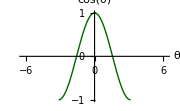

```mathematica
Plot[Cos[θ],{θ,-π,π},
AxesLabel->Automatic,
PlotLabel->Cos[θ],
PlotStyle->Darker[Green,3/5],
PlotPoints->2,
PlotRange->{{-2π,2π},Automatic},
ImageSize->Small
]
```

Note: I also added the “PlotLabel” option.  This is a very important option when presenting your work.

Note: Intending to make the plot jagged, I used the minimum number of plot points.  In this case, it doesn’t alter the plot.

### 2) Create a 3D plot of a sphere with similar options as above.

```mathematica
Plot3D[Cos[ω θ],{θ,-π,π},{ω,-5,5},
AxesLabel->Automatic,
PlotLabel->Cos[θ],
PlotStyle->Darker[Green,3/5],
PlotPoints->2,
PlotRange->{{-2π,2π},Automatic},
ImageSize->Small
]
```

-Graphics3D-

### 3) Create a table of odd number between 3 and 71.

```mathematica
Table[2k+1,{k,1,70/2}]
```

{3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71}

### 4) Create a set of pairs of real numbers, such that when plotted they form a line.

{{-10,-29},{-9,-26},{-8,-23},{-7,-20},{-6,-17},{-5,-14},{-4,-11},{-3,-8},{-2,-5},{-1,-2},{0,1},{1,4},{2,7},{3,10},{4,13},{5,16},{6,19},{7,22},{8,25},{9,28},{10,31}}

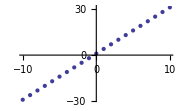

```mathematica
Table[{n,3n+1},{n,-10,10}]
ListPlot[%,ImageSize->Small]
```

### 5) Simplify and then fully simplify the solutions to exercises 6-8, 14-15 from section 13.

#### 6)

```mathematica
Simplify[-1/(-1+x)+x/(-1+x)^2]
FullSimplify[-1/(-1+x)+x/(-1+x)^2]
```

1/(-1+x)^2

1/(-1+x)^2

#### 7)

```mathematica
Simplify[Gamma[1+n] PolyGamma[0,1+n]]
FullSimplify[Gamma[1+n] PolyGamma[0,1+n]]
```

Gamma[1+n] PolyGamma[0,1+n]

Gamma[1+n] PolyGamma[0,1+n]

#### 8)

```mathematica
Simplify[-1/(-1+x)]
FullSimplify[-1/(-1+x)]
```

1/(1-x)

1/(1-x)

#### 14)

```mathematica
Simplify[{{u[x]->-(A (ⅇ^(((-B-√(4 A+B^2-4 A C)) x)/(2 A))-ⅇ^(((-B+√(4 A+B^2-4 A C)) x)/(2 A))) Γ)/(√(4 A+B^2-4 A C))}}]
FullSimplify[{{u[x]->-(A (ⅇ^(((-B-√(4 A+B^2-4 A C)) x)/(2 A))-ⅇ^(((-B+√(4 A+B^2-4 A C)) x)/(2 A))) Γ)/(√(4 A+B^2-4 A C))}}]
```

{{u[x]→(A ⅇ^(-((B+√(4 A+B^2-4 A C)) x)/(2 A)) (-1+ⅇ^((√(4 A+B^2-4 A C) x)/A)) Γ)/(√(B^2-4 A (-1+C)))}}

{{u[x]→(A ⅇ^(-((B+√(B^2-4 A (-1+C))) x)/(2 A)) (-1+ⅇ^((√(4 A+B^2-4 A C) x)/A)) Γ)/(√(B^2-4 A (-1+C)))}}

#### 15)

```mathematica
Simplify[{{μ->(7 ⅇ^(((-1+C) x)/A+((-1+C) (A t-B x))/(A B)))/(ⅇ^(((-1+C) x)/A+((-1+C) (A t-B x))/(A B))-f[-(A t-B x)/B])}}]
FullSimplify[{{μ->(7 ⅇ^(((-1+C) x)/A+((-1+C) (A t-B x))/(A B)))/(ⅇ^(((-1+C) x)/A+((-1+C) (A t-B x))/(A B))-f[-(A t-B x)/B])}}]
```

{{μ→(7 ⅇ^(((-1+C) t)/B))/(ⅇ^(((-1+C) t)/B)-f[-(A t)/B+x])}}

{{μ→1/(1/7-1/7 ⅇ^((t-C t)/B) f[-(A t)/B+x])}}

### 6) For the solutions to each of the parts to the previous problem, create a scaling coefficient on some part of the solution. Then create a manipulatable plot for each solution and explore the di.0berent results.

#### 6)

```mathematica
Manipulate[
Plot[1/(-1+μ x)^2,{x,-2,2},PlotRange->{Automatic,10},ImageSize->Small],
{μ,-1,1}
]
```

#### 7)

```mathematica
Manipulate[
Plot[Gamma[1+γ n] PolyGamma[0,1+γ n],{n,0,3},PlotRange->{Automatic,{-10,10}},ImageSize->Small],
{γ,-1,1}
]
```

#### 8)

```mathematica
Manipulate[
Plot[1/(1-ζ x),{x,-1,1},PlotRange->Max[Table[1/(1-ζ x),{x,-1,1}]],ImageSize->Small],
{ζ,-100,100}
]
```

#### 14)

```mathematica
Manipulate[
Plot[(A ⅇ^(-((B+√(B^2-4 A (-1+C))) x)/(2 A)) (-1+ⅇ^((√(4 A+B^2-4 A C) x)/A)) Γ)/(√(B^2-4 A (-1+C))),{x,-1,1},PlotRange->Max[Table[Abs[(A ⅇ^(-((B+√(B^2-4 A (-1+C))) x)/(2 A)) (-1+ⅇ^((√(4 A+B^2-4 A C) x)/A)) Γ)/(√(B^2-4 A (-1+C)))],{x,-1,1}]],ImageSize->Small],
{A,-1,1},
{B,-1,1},
{C,-1,1},
{Γ,-1,1}
]
```

#### 15)

```mathematica
Manipulate[
Plot[1/(1/7-1/7 ⅇ^((t-C t)/B) f[-(A t)/B+x]),{x,-1,1},ImageSize->Small],
{A,-1,1},
{B,-1,1},
{C,-1,1},
{t,-1,1},
{f,{Cos,Sin}}
]
```

### 5) Make a GIF of a parabola that changes its curvature.

```mathematica
SetDirectory[NotebookDirectory[]]
Table[Plot[μ x^2,{x,-1,1},PlotRange->1],{μ,-1,1,.05}];
Export["Parabola.gif",%]
```

U:\Science\Mathematica for the Constantly Busy\Solutions

Parabola.gif